## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Generate global Har translation decay plots

### Reading In Files

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = Table[FileNames[(myFolders[[i]]<>"/*_ySpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myYellowOnlyFiles
```

5

```mathematica
myWhiteFiles = Table[FileNames[(myFolders[[i]]<>"/*_wSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myWhiteFiles
```

5

```mathematica
myAllYellowFiles = Table[FileNames[(myFolders[[i]]<>"/*_gSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myAllYellowFiles
```

5

```mathematica
myPurpleFiles = Table[FileNames[(myFolders[[i]]<>"/*_brSpotNTime.m")],{i,1,Length@myFolders,1}];
Length@myPurpleFiles
```

5

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Table[Import[myYellowOnlyFiles⟦i,j⟧],{j,1,Length@myYellowOnlyFiles⟦i⟧,1}],{i,1,Length@myYellowOnlyFiles,1}]//#[[2;;3]]&//Flatten[#,1]& ;
```

```mathematica
cellCount = Length@onlyYellow
```

6

```mathematica
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

{{-178,65},{-118,61},{-58,57},{2,62},{62,55},{122,51},{182,49},{242,59},{302,59},{362,48},{422,41},{482,43},{542,40},{602,35},{662,28},{722,34},{782,33},{842,34},{902,34},{962,26},{1022,28},{1082,26},{1142,33},{1202,19},{1262,29},{1322,27},{1382,27},{1442,29},{1502,28},{1562,25},{1622,20},{1682,21},{1742,26},{1802,25},{1862,17},{1922,18},{1982,27},{2042,21},{2102,19},{2162,14},{2222,25},{2282,19},{2342,16},{2402,17},{2462,13},{2522,20},{2582,14},{2642,12},{2702,15},{2762,13},{2822,13},{2882,18},{2942,13},{3002,15},{3062,17},{3122,10},{3182,11},{3242,13},{3302,13},{3362,13},{3422,10},{3482,6},{3542,10},{3602,17},{3662,8}}

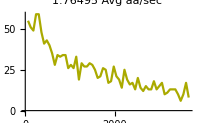
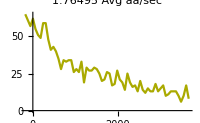
{{1.76495,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
ySpotNTime>>analysisFolder<>"_OnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Table[Import[myAllYellowFiles[[i,j]]],{j,1,Length@myAllYellowFiles[[i]],1}],{i,1,Length@myAllYellowFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@allYellow
```

6

```mathematica
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

{{-178,109},{-118,103},{-58,91},{2,91},{62,92},{122,79},{182,86},{242,87},{302,88},{362,79},{422,69},{482,63},{542,70},{602,67},{662,54},{722,64},{782,65},{842,59},{902,61},{962,51},{1022,49},{1082,51},{1142,53},{1202,44},{1262,55},{1322,53},{1382,55},{1442,48},{1502,50},{1562,50},{1622,40},{1682,42},{1742,47},{1802,42},{1862,33},{1922,40},{1982,42},{2042,37},{2102,33},{2162,29},{2222,39},{2282,34},{2342,29},{2402,27},{2462,30},{2522,32},{2582,30},{2642,29},{2702,27},{2762,26},{2822,20},{2882,29},{2942,22},{3002,26},{3062,25},{3122,13},{3182,18},{3242,19},{3302,21},{3362,16},{3422,13},{3482,13},{3542,14},{3602,21},{3662,15}}

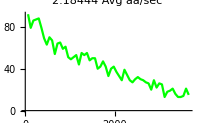
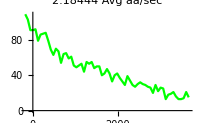
{{2.18444,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",yelAllTimePlot];
ySpotNTime>>analysisFolder<>"_yAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Table[Import[myWhiteFiles[[i,j]]],{j,1,Length@myWhiteFiles[[i]],1}],{i,1,Length@myWhiteFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@white
```

6

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
whiteSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

{{-178,44},{-118,42},{-58,34},{2,29},{62,37},{122,28},{182,37},{242,28},{302,29},{362,31},{422,28},{482,20},{542,30},{602,32},{662,26},{722,30},{782,32},{842,25},{902,27},{962,25},{1022,21},{1082,25},{1142,20},{1202,25},{1262,26},{1322,26},{1382,28},{1442,19},{1502,22},{1562,25},{1622,20},{1682,21},{1742,21},{1802,17},{1862,16},{1922,22},{1982,15},{2042,16},{2102,14},{2162,15},{2222,14},{2282,15},{2342,13},{2402,10},{2462,17},{2522,12},{2582,16},{2642,17},{2702,12},{2762,13},{2822,7},{2882,11},{2942,9},{3002,11},{3062,8},{3122,3},{3182,7},{3242,6},{3302,8},{3362,3},{3422,3},{3482,7},{3542,4},{3602,4},{3662,7}}

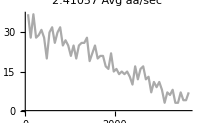
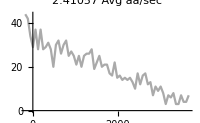
{{2.41057,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",whiteTimePlot];
ySpotNTime>>analysisFolder<>"_wGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Table[Import[myPurpleFiles[[i,j]]],{j,1,Length@myPurpleFiles[[i]],1}],{i,1,Length@myPurpleFiles,1}]//#[[2;;3]]&//Flatten[#,1]&;
```

```mathematica
cellCount = Length@purple
```

6

```mathematica
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
times = Total[Transpose[purple],{2}]//#[[All,1]]/cellCount&;
purpleSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*)
```

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

{{-178,151},{-118,152},{-58,128},{2,130},{62,142},{122,142},{182,144},{242,150},{302,141},{362,145},{422,134},{482,154},{542,146},{602,145},{662,157},{722,138},{782,155},{842,151},{902,157},{962,149},{1022,136},{1082,146},{1142,138},{1202,149},{1262,149},{1322,151},{1382,153},{1442,145},{1502,168},{1562,154},{1622,155},{1682,139},{1742,144},{1802,134},{1862,137},{1922,131},{1982,141},{2042,148},{2102,150},{2162,149},{2222,134},{2282,160},{2342,150},{2402,154},{2462,144},{2522,158},{2582,149},{2642,157},{2702,148},{2762,142},{2822,149},{2882,145},{2942,143},{3002,164},{3062,146},{3122,148},{3182,151},{3242,132},{3302,136},{3362,138},{3422,157},{3482,153},{3542,144},{3602,141},{3662,152}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

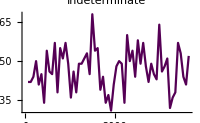
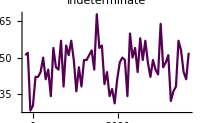
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",purpleTimePlot];
ySpotNTime>>analysisFolder<>"_pGlobalTime.m"
```

### View it all...

```mathematica
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot
}]
```

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots//TableForm
```

6 | 8 | 7 | 6 | 5 | 7 | 5 | 8 | 11 | 7 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 5 | 5 | 5 | 4 | 5 | 3 | 5 | 2 | 4 | 5 | 5 | 5 | 5 | 4 | 2 | 3 | 6 | 3 | 1 | 6 | 3 | 7 | 1 | 7 | 5 | 4 | 2 | 2 | 4 | 3 | 1 | 4 | 3 | 2 | 6 | 4 | 4 | 1 | 4 | 1 | 4 | 5 | 5 | 2 | 2 | 2 | 3 | 1
14 | 15 | 12 | 15 | 15 | 7 | 10 | 12 | 6 | 12 | 12 | 14 | 11 | 10 | 6 | 12 | 11 | 10 | 8 | 7 | 9 | 9 | 11 | 3 | 8 | 8 | 4 | 3 | 9 | 7 | 7 | 5 | 9 | 10 | 7 | 5 | 8 | 2 | 4 | 4 | 4 | 4 | 6 | 3 | 4 | 4 | 4 | 3 | 5 | 1 | 4 | 3 | 3 | 5 | 7 | 1 | 2 | 3 | 4 | 2 | 1 | 0 | 1 | 4 | 2
3 | 1 | 2 | 1 | 5 | 4 | 1 | 2 | 5 | 2 | 2 | 5 | 2 | 2 | 1 | 3 | 1 | 2 | 1 | 1 | 1 | 0 | 2 | 4 | 7 | 1 | 1 | 2 | 3 | 1 | 0 | 1 | 3 | 1 | 0 | 1 | 3 | 0 | 0 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 0 | 1 | 1 | 3 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 4 | 0
7 | 5 | 10 | 10 | 9 | 7 | 7 | 6 | 8 | 8 | 7 | 6 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 3 | 5 | 4 | 4 | 2 | 1 | 3 | 4 | 5 | 2 | 2 | 3 | 3 | 3 | 0 | 2 | 3 | 3 | 3 | 2 | 1 | 3 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 0 | 1
26 | 25 | 19 | 20 | 14 | 19 | 21 | 16 | 22 | 13 | 9 | 8 | 10 | 9 | 5 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 8 | 4 | 8 | 6 | 7 | 9 | 5 | 7 | 3 | 5 | 6 | 6 | 4 | 4 | 5 | 7 | 4 | 5 | 6 | 2 | 2 | 5 | 2 | 8 | 2 | 5 | 2 | 5 | 2 | 4 | 4 | 5 | 4 | 3 | 4 | 2 | 1 | 4 | 3 | 2 | 3 | 3 | 3
9 | 7 | 7 | 10 | 7 | 7 | 5 | 15 | 7 | 6 | 7 | 7 | 7 | 2 | 6 | 4 | 5 | 4 | 7 | 3 | 3 | 2 | 5 | 1 | 3 | 5 | 6 | 5 | 4 | 3 | 3 | 5 | 2 | 2 | 1 | 4 | 2 | 6 | 2 | 2 | 4 | 4 | 1 | 4 | 3 | 0 | 3 | 0 | 2 | 2 | 3 | 1 | 1 | 0 | 2 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 2 | 3 | 1

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{3.03363,3.46952,2.07401,2.45678,1.98417,1.92152,2.47891,2.38107,2.47114,1.87833,1.21465,1.43635,1.21894,1.37164,0.73433,0.949827,1.05947,1.22704,0.919649,0.927789,0.951657,1.08515,1.29777,0.564742,1.1203,0.841834,0.708099,0.708663,0.770236,0.944315,0.753451,0.650793,1.09313,1.33357,0.904808,0.709721,0.992243,0.881573,0.78721,0.747516,0.849761,0.494575,0.610388,0.599302,0.406681,0.923926,0.613284,0.636883,0.597702,0.602914,0.441176,0.689179,0.595561,0.874208,0.881573,0.613831,0.514167,0.3554,0.608292,0.588008,0.299851,0.364623,0.357549,0.61487,0.356476}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{10.3333,8.66667,6.66667,6.33333,11.6667,10.1667,7.16667,12.5,16.,13.6667,17.8333,7.33333,9.5,17.6667,8.5,13.1667,12.1667,12.8333,10.3333,12.5,6.83333,11.,10.8333,9.16667,10.1667,8.5,14.3333,12.6667,11.8333,9.33333}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{ySpotNTime,errorBS}];
```

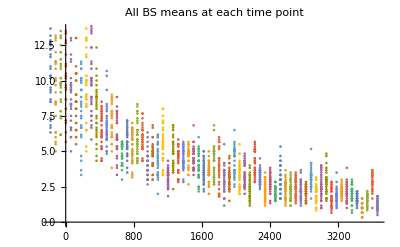

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

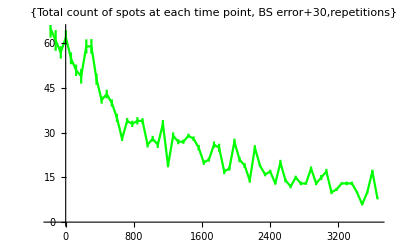

```mathematica
ErrorListPlot[b,PlotStyle->{Green}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```